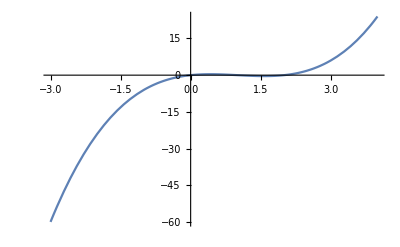

```mathematica
Plot[FactorialPower[x,3],{x,-3,4}]
```

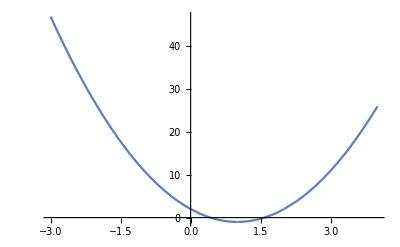

```mathematica
(* Now, plot the derivative!*)
f[x_,n_]:=FactorialPower[x,n]*(Sum[1/(x-k),{k,0,n-1}])
Plot[f[x,3],{x,-3,4}]
```

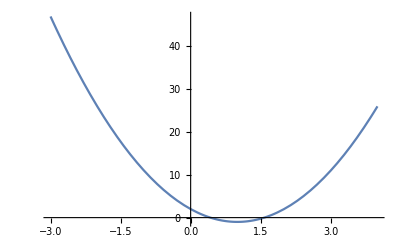

```mathematica
Plot[2-6x+3x^2,{x,-3,4}]
```

```mathematica
f[0,3]
```

f[0,3]

```mathematica
f[1]
f[2]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
f[1/2]
```

-1/4

```mathematica
Limit[f[x],x->0]
Limit[f[x],x->1]
Limit[f[x],x->2]
```

2

-1

2

```mathematica
(* Now, try it with the limit... *)
g[x_]:=Limit[f[y],y->x]
```

```mathematica
g[0]
g[1]
g[2]
```

2

-1

2

```mathematica
Plot[g[x],{x,-3,4}]
```

-Graphics-

```mathematica
(g[x])'
```

((1/(-2+x)+1/(-1+x)+1/x) FactorialPower[x,3])'

```mathematica
FactorialPower[7,7]
```

5040

```mathematica
(* Just curious... *)
genB[x_,y_]:=Gamma[y+1]/(Gamma[x+1]*Gamma[y-x+1])
Plot3D[genB[x,y],{x,-5,5},{y,-5,5}]
```

```mathematica
Integrate[FactorialPower[x,n],x]
```

∫FactorialPower[x,n]ⅆx